```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY189/morning_sec_int_data/862nm.dat"]
```

{{1.12389,-0.17251},{1.13423,-0.159136},{1.14739,-0.145049},{1.16401,-0.136278},{1.183,-0.151474},{1.20042,-0.137516},{1.22646,-0.136954},{1.24828,-0.155228},{1.27782,-0.149266},{1.30453,-0.168123},{1.34407,-0.136759},{1.38078,-0.15059},{1.41705,-0.159218},{1.46132,-0.172486},{1.51023,-0.174246},{1.58758,-0.175294},{1.63065,-0.15711}}

-0.102198-0.0402779 x

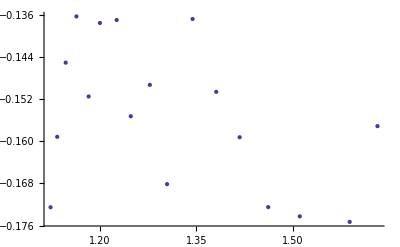

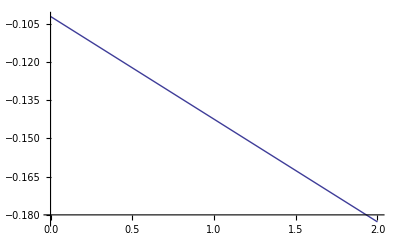

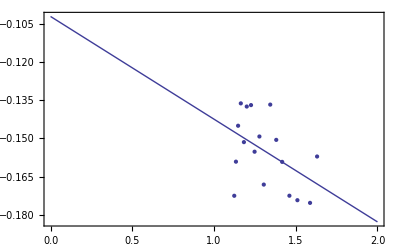

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```